# Quantum Random Walk

```mathematica
Clear["Global`*"]
```

```mathematica
Needs["Quantum`Notation`"]
```

Quantum`Notation` 
A Mathematica package for Quantum calculations in Dirac bra-ket notation
by José Luis Gómez-Muñoz

This add-on does NOT work properly with the debugger turned on. Therefore the debugger must NOT be checked in the Evaluation menu of Mathematica.
Execute SetQuantumAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetQuantumAliases[] must be executed again in each new notebook that is created, only one time per notebook.

MATHEMATICA 11.3.0 for Mac OS X x86 (64-bit) (March 7, 2018)

QUANTUM version EN CONSTRUCCION

TODAY IS Tue 4 Jun 2019 21:59:16

```mathematica
SetQuantumAliases[];
```

```mathematica
|w[0]⟩=|Subscript[0, ĉ]⟩⊗|Subscript[0, p̂]⟩
```

|0_(ĉ),0_(p̂)⟩

```mathematica
(*Define Hadmard Gate*)
```

```mathematica
Ry[θ_]=Cos[θ/2]|Subscript[0, ĉ]⟩·⟨Subscript[0, ĉ]|+Sin[θ/2]|Subscript[1, ĉ]⟩·⟨Subscript[0, ĉ]|-Sin[θ/2]|Subscript[0, ĉ]⟩·⟨Subscript[1, ĉ]|+Cos[θ/2]|Subscript[1, ĉ]⟩·⟨Subscript[1, ĉ]|
```

Cos[θ/2] |0_(ĉ)⟩·⟨0_(ĉ)|+Sin[θ/2] |1_(ĉ)⟩·⟨0_(ĉ)|-Sin[θ/2] |0_(ĉ)⟩·⟨1_(ĉ)|+Cos[θ/2] |1_(ĉ)⟩·⟨1_(ĉ)|

```mathematica
(*Move operator, coin=0, move backward; coin=1, move forward*)
```

```mathematica
Tup=|Subscript[0, ĉ]⟩·⟨Subscript[0, ĉ]|⊗∑_(j=-∞)^∞ (|Subscript[(j+1), p̂]⟩·⟨Subscript[j, p̂]|)+|Subscript[1, ĉ]⟩·⟨Subscript[1, ĉ]|⊗Subscript[1, p̂]
```

∑_(j=-∞)^∞ |0_(ĉ),(1+j)_(p̂)⟩·⟨0_(ĉ),j_(p̂)|+|1_(ĉ)⟩·⟨1_(ĉ)|·1_(p̂)

```mathematica
Tdown=|Subscript[1, ĉ]⟩·⟨Subscript[1, ĉ]|⊗∑_(j=-∞)^∞ (|Subscript[(j-1), p̂]⟩·⟨Subscript[j, p̂]|)+|Subscript[0, ĉ]⟩·⟨Subscript[0, ĉ]|⊗Subscript[ℐ, p̂]
```

∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|+|0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)

```mathematica
Expand[Tup·|w[0]⟩]
```

|1_(ĉ)⟩·⟨1_(ĉ)|·1_(p̂)·|0_(ĉ),0_(p̂)⟩+|0_(ĉ),1_(p̂)⟩

```mathematica
steps=20;
θ1 = -Pi/2;
θ2 = 0;
increment = Pi/steps;
Do[θ2 = θ2 + increment,
|w[k]⟩=Expand[Tdown·(Ry[θ2]·(Tup·(Ry[θ1]·|w[k-1]⟩)))]//N,
{k,1,steps}]
```

Do::nliter: Non-list iterator |w[k]⟩=N[Expand[Tdown·(Ry[θ2]·(Tup·(Ry[«1»]·|«1»⟩)))]] at position 2 does not evaluate to a real numeric value.

Do[θ2=θ2+increment,|w[k]⟩=N[Expand[Tdown·(Ry[θ2]·(Tup·(Ry[θ1]·|w[k-1]⟩)))]],{k,1,steps}]

```mathematica
|w[2]⟩=Expand[Tdown·(Ry[θ2]·(Tup·(Ry[θ1]·|w[1]⟩)))]
```

-1/2 ∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|·ℐ_(p̂)·(|0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|0_(ĉ),1_(p̂)⟩-|1_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|0_(ĉ),1_(p̂)⟩)+1/2 ∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|·ℐ_(p̂)·(|0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|0_(ĉ),0_(p̂)⟩-|1_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|0_(ĉ),0_(p̂)⟩)-1/2 ∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|·ℐ_(p̂)·(|0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|1_(ĉ),0_(p̂)⟩-|1_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|1_(ĉ),0_(p̂)⟩)-1/2 ∑_(j6865=-∞)^∞ |0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|0_(ĉ),j6865_(p̂)⟩·⟨1_(ĉ),j6865_(p̂)|·ℐ_(p̂)·|0_(ĉ),0_(p̂)⟩+1/2 ∑_(j=-∞)^∞ |0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|0_(ĉ),(1+j)_(p̂)⟩·⟨0_(ĉ),j_(p̂)|·ℐ_(p̂)·|0_(ĉ),1_(p̂)⟩+1/2 ∑_(j6881=-∞)^∞ |0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|0_(ĉ),j6881_(p̂)⟩·⟨1_(ĉ),j6881_(p̂)|·ℐ_(p̂)·|1_(ĉ),0_(p̂)⟩-1/2 ∑_(j=-∞)^∞ |0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|0_(ĉ),(1+j)_(p̂)⟩·⟨0_(ĉ),j_(p̂)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|0_(ĉ),0_(p̂)⟩+1/2 ∑_(j=-∞)^∞ |0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|0_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|·ℐ_(p̂)·|0_(ĉ),0_(p̂)⟩-1/2 ∑_(j=-∞)^∞ |0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|·ℐ_(p̂)·|0_(ĉ),0_(p̂)⟩+1/2 ∑_(j=-∞)^∞ |0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|0_(ĉ),(1+j)_(p̂)⟩·⟨0_(ĉ),j_(p̂)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|1_(ĉ),0_(p̂)⟩-1/2 ∑_(j=-∞)^∞ |0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|0_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|·ℐ_(p̂)·|1_(ĉ),0_(p̂)⟩+1/2 ∑_(j=-∞)^∞ |0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|·ℐ_(p̂)·|1_(ĉ),0_(p̂)⟩+1/2 (∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·∑_(j=-∞)^∞ |0_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|·ℐ_(p̂)·|0_(ĉ),0_(p̂)⟩-1/2 (∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|·ℐ_(p̂)·|0_(ĉ),0_(p̂)⟩-1/2 (∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·∑_(j=-∞)^∞ |0_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|·ℐ_(p̂)·|1_(ĉ),0_(p̂)⟩+1/2 (∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|·ℐ_(p̂)·|1_(ĉ),0_(p̂)⟩+1/2 (∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|)·|0_(ĉ)⟩·⟨0_(ĉ)|·(∑_(j=-∞)^∞ |0_(ĉ),(1+j)_(p̂)⟩·⟨0_(ĉ),j_(p̂)|)·|0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|0_(ĉ),1_(p̂)⟩-1/2 (∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|)·|1_(ĉ)⟩·⟨1_(ĉ)|·(∑_(j=-∞)^∞ |0_(ĉ),(1+j)_(p̂)⟩·⟨0_(ĉ),j_(p̂)|)·|0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|0_(ĉ),1_(p̂)⟩-1/2 (∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|)·|0_(ĉ)⟩·⟨0_(ĉ)|·(∑_(j=-∞)^∞ |0_(ĉ),(1+j)_(p̂)⟩·⟨0_(ĉ),j_(p̂)|)·|1_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|0_(ĉ),1_(p̂)⟩+1/2 (∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|)·|1_(ĉ)⟩·⟨1_(ĉ)|·(∑_(j=-∞)^∞ |0_(ĉ),(1+j)_(p̂)⟩·⟨0_(ĉ),j_(p̂)|)·|1_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|0_(ĉ),1_(p̂)⟩-1/2 |0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|0_(ĉ),1_(p̂)⟩+1/2 |0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|0_(ĉ),1_(p̂)⟩-1/2 (∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|)·|0_(ĉ)⟩·⟨0_(ĉ)|·(∑_(j=-∞)^∞ |0_(ĉ),(1+j)_(p̂)⟩·⟨0_(ĉ),j_(p̂)|)·|0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|0_(ĉ),0_(p̂)⟩+1/2 (∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|)·|1_(ĉ)⟩·⟨1_(ĉ)|·(∑_(j=-∞)^∞ |0_(ĉ),(1+j)_(p̂)⟩·⟨0_(ĉ),j_(p̂)|)·|0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|0_(ĉ),0_(p̂)⟩+1/2 (∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|)·|0_(ĉ)⟩·⟨0_(ĉ)|·(∑_(j=-∞)^∞ |0_(ĉ),(1+j)_(p̂)⟩·⟨0_(ĉ),j_(p̂)|)·|1_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|0_(ĉ),0_(p̂)⟩-1/2 (∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|)·|1_(ĉ)⟩·⟨1_(ĉ)|·(∑_(j=-∞)^∞ |0_(ĉ),(1+j)_(p̂)⟩·⟨0_(ĉ),j_(p̂)|)·|1_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|0_(ĉ),0_(p̂)⟩+1/2 (∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|)·|0_(ĉ)⟩·⟨0_(ĉ)|·(∑_(j=-∞)^∞ |0_(ĉ),(1+j)_(p̂)⟩·⟨0_(ĉ),j_(p̂)|)·|0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|1_(ĉ),0_(p̂)⟩-1/2 (∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|)·|1_(ĉ)⟩·⟨1_(ĉ)|·(∑_(j=-∞)^∞ |0_(ĉ),(1+j)_(p̂)⟩·⟨0_(ĉ),j_(p̂)|)·|0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|1_(ĉ),0_(p̂)⟩-1/2 (∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|)·|0_(ĉ)⟩·⟨0_(ĉ)|·(∑_(j=-∞)^∞ |0_(ĉ),(1+j)_(p̂)⟩·⟨0_(ĉ),j_(p̂)|)·|1_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|1_(ĉ),0_(p̂)⟩+1/2 (∑_(j=-∞)^∞ |1_(ĉ),(-1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|)·|1_(ĉ)⟩·⟨1_(ĉ)|·(∑_(j=-∞)^∞ |0_(ĉ),(1+j)_(p̂)⟩·⟨0_(ĉ),j_(p̂)|)·|1_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|1_(ĉ),0_(p̂)⟩+1/2 |0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|0_(ĉ),0_(p̂)⟩-1/2 |0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|0_(ĉ),0_(p̂)⟩-1/2 |0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|1_(ĉ),0_(p̂)⟩+1/2 |0_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨0_(ĉ)|·ℐ_(p̂)·|1_(ĉ)⟩·⟨1_(ĉ)|·ℐ_(p̂)·|1_(ĉ),0_(p̂)⟩

```mathematica
k
```

k

```mathematica
|w[3]⟩
```

(|0_(ĉ),-3_(p̂)⟩)/(2 √2)+(|0_(ĉ),-1_(p̂)⟩)/(√2)-(|0_(ĉ),1_(p̂)⟩)/(2 √2)+(|1_(ĉ),-1_(p̂)⟩)/(2 √2)+(|1_(ĉ),3_(p̂)⟩)/(2 √2)

```mathematica
|w[5]⟩
```

(|0_(ĉ),-5_(p̂)⟩)/(4 √2)+(|0_(ĉ),-3_(p̂)⟩)/(√2)-(|0_(ĉ),3_(p̂)⟩)/(4 √2)+(|1_(ĉ),-3_(p̂)⟩)/(4 √2)+(|1_(ĉ),-1_(p̂)⟩)/(2 √2)-(|1_(ĉ),1_(p̂)⟩)/(2 √2)+(|1_(ĉ),3_(p̂)⟩)/(2 √2)+(|1_(ĉ),5_(p̂)⟩)/(4 √2)

```mathematica
pp[j_]:=|Subscript[0, ĉ],Subscript[j, p̂]⟩·⟨Subscript[0, ĉ],Subscript[j, p̂]|+|Subscript[1, ĉ],Subscript[j, p̂]⟩·⟨Subscript[1, ĉ],Subscript[j, p̂]|
```

```mathematica
probabilities=Table[{j,⟨w[steps]|·pp[j]·|w[steps]⟩},{j,-steps,steps}]
```

{{-20,1/1048576},{-19,0},{-18,181/524288},{-17,0},{-16,9257/524288},{-15,0},{-14,95617/524288},{-13,0},{-12,295265/1048576},{-11,0},{-10,965/32768},{-9,0},{-8,2501/32768},{-7,0},{-6,2377/32768},{-5,0},{-4,11221/262144},{-3,0},{-2,4165/131072},{-1,0},{0,3969/131072},{1,0},{2,3969/131072},{3,0},{4,7301/262144},{5,0},{6,637/32768},{7,0},{8,485/32768},{9,0},{10,1361/32768},{11,0},{12,28097/1048576},{13,0},{14,33317/524288},{15,0},{16,5417/524288},{17,0},{18,145/524288},{19,0},{20,1/1048576}}

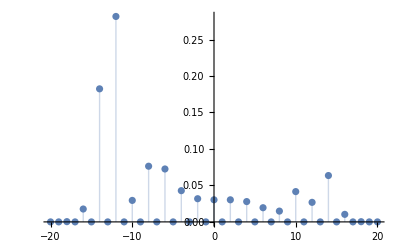

```mathematica
ListPlot[probabilities,PlotRange->All,Filling->Axis]
```

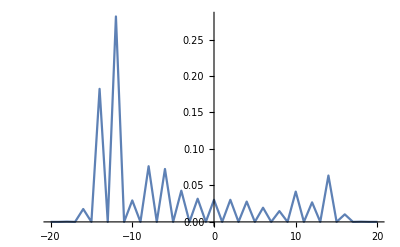

```mathematica
ListPlot[probabilities,PlotRange->All,Joined->True]
```

```mathematica
qm= QuantumMeasurement[|w[steps]⟩,{p̂},FactorKet->False]
```

Probability | Measurement | State
1/1048576 | {{-20_(p̂)}} | |0_(ĉ),-20_(p̂)⟩
181/524288 | {{-18_(p̂)}} | (19 |0_(ĉ),-18_(p̂)⟩+|1_(ĉ),-18_(p̂)⟩)/(√362)
9257/524288 | {{-16_(p̂)}} | (135 |0_(ĉ),-16_(p̂)⟩+17 |1_(ĉ),-16_(p̂)⟩)/(√18514)
95617/524288 | {{-14_(p̂)}} | (425 |0_(ĉ),-14_(p̂)⟩+103 |1_(ĉ),-14_(p̂)⟩)/(√191234)
295265/1048576 | {{-12_(p̂)}} | (484 |0_(ĉ),-12_(p̂)⟩+247 |1_(ĉ),-12_(p̂)⟩)/(√295265)
965/32768 | {{-10_(p̂)}} | (-33 |0_(ĉ),-10_(p̂)⟩+29 |1_(ĉ),-10_(p̂)⟩)/(√1930)
2501/32768 | {{-8_(p̂)}} | -(49 |0_(ĉ),-8_(p̂)⟩+51 |1_(ĉ),-8_(p̂)⟩)/(√5002)
2377/32768 | {{-6_(p̂)}} | (65 |0_(ĉ),-6_(p̂)⟩+23 |1_(ĉ),-6_(p̂)⟩)/(√4754)
11221/262144 | {{-4_(p̂)}} | (-15 |0_(ĉ),-4_(p̂)⟩+2 |1_(ĉ),-4_(p̂)⟩)/(√229)
4165/131072 | {{-2_(p̂)}} | (11 |0_(ĉ),-2_(p̂)⟩-7 |1_(ĉ),-2_(p̂)⟩)/(√170)
3969/131072 | {{0_(p̂)}} | (-|0_(ĉ),0_(p̂)⟩+|1_(ĉ),0_(p̂)⟩)/(√2)
3969/131072 | {{2_(p̂)}} | (|0_(ĉ),2_(p̂)⟩-|1_(ĉ),2_(p̂)⟩)/(√2)
7301/262144 | {{4_(p̂)}} | (-10 |0_(ĉ),4_(p̂)⟩+7 |1_(ĉ),4_(p̂)⟩)/(√149)
637/32768 | {{6_(p̂)}} | (5 |0_(ĉ),6_(p̂)⟩-|1_(ĉ),6_(p̂)⟩)/(√26)
485/32768 | {{8_(p̂)}} | -(21 |0_(ĉ),8_(p̂)⟩+23 |1_(ĉ),8_(p̂)⟩)/(√970)
1361/32768 | {{10_(p̂)}} | (-11 |0_(ĉ),10_(p̂)⟩+51 |1_(ĉ),10_(p̂)⟩)/(√2722)
28097/1048576 | {{12_(p̂)}} | (121 |0_(ĉ),12_(p̂)⟩-116 |1_(ĉ),12_(p̂)⟩)/(√28097)
33317/524288 | {{14_(p̂)}} | (75 |0_(ĉ),14_(p̂)⟩-247 |1_(ĉ),14_(p̂)⟩)/(√66634)
5417/524288 | {{16_(p̂)}} | (15 |0_(ĉ),16_(p̂)⟩-103 |1_(ĉ),16_(p̂)⟩)/(√10834)
145/524288 | {{18_(p̂)}} | (|0_(ĉ),18_(p̂)⟩-17 |1_(ĉ),18_(p̂)⟩)/(√290)
1/1048576 | {{20_(p̂)}} | -|1_(ĉ),20_(p̂)⟩
Probability | Measurement | State

```mathematica
N[qm]
```

Probability | Measurement | State
9.53674×10^-7 | {{-20_(p̂)}} | |0_(ĉ),-20_(p̂)⟩
0.00034523 | {{-18_(p̂)}} | 0.0525588 (19. |0_(ĉ),-18_(p̂)⟩+|1_(ĉ),-18_(p̂)⟩)
0.0176563 | {{-16_(p̂)}} | 0.00734937 (135. |0_(ĉ),-16_(p̂)⟩+17. |1_(ĉ),-16_(p̂)⟩)
0.182375 | {{-14_(p̂)}} | 0.00228674 (425. |0_(ĉ),-14_(p̂)⟩+103. |1_(ĉ),-14_(p̂)⟩)
0.281587 | {{-12_(p̂)}} | 0.00184032 (484. |0_(ĉ),-12_(p̂)⟩+247. |1_(ĉ),-12_(p̂)⟩)
0.0294495 | {{-10_(p̂)}} | 0.0227626 (-33. |0_(ĉ),-10_(p̂)⟩+29. |1_(ĉ),-10_(p̂)⟩)
0.0763245 | {{-8_(p̂)}} | -0.0141393 (49. |0_(ĉ),-8_(p̂)⟩+51. |1_(ĉ),-8_(p̂)⟩)
0.0725403 | {{-6_(p̂)}} | 0.0145034 (65. |0_(ĉ),-6_(p̂)⟩+23. |1_(ĉ),-6_(p̂)⟩)
0.0428047 | {{-4_(p̂)}} | 0.0660819 (-15. |0_(ĉ),-4_(p̂)⟩+2. |1_(ĉ),-4_(p̂)⟩)
0.0317764 | {{-2_(p̂)}} | 0.0766965 (11. |0_(ĉ),-2_(p̂)⟩-7. |1_(ĉ),-2_(p̂)⟩)
0.0302811 | {{0_(p̂)}} | 0.707107 (-1. |0_(ĉ),0_(p̂)⟩+|1_(ĉ),0_(p̂)⟩)
0.0302811 | {{2_(p̂)}} | 0.707107 (|0_(ĉ),2_(p̂)⟩-1. |1_(ĉ),2_(p̂)⟩)
0.0278511 | {{4_(p̂)}} | 0.0819232 (-10. |0_(ĉ),4_(p̂)⟩+7. |1_(ĉ),4_(p̂)⟩)
0.0194397 | {{6_(p̂)}} | 0.196116 (5. |0_(ĉ),6_(p̂)⟩-1. |1_(ĉ),6_(p̂)⟩)
0.014801 | {{8_(p̂)}} | -0.0321081 (21. |0_(ĉ),8_(p̂)⟩+23. |1_(ĉ),8_(p̂)⟩)
0.0415344 | {{10_(p̂)}} | 0.0191671 (-11. |0_(ĉ),10_(p̂)⟩+51. |1_(ĉ),10_(p̂)⟩)
0.0267954 | {{12_(p̂)}} | 0.00596582 (121. |0_(ĉ),12_(p̂)⟩-116. |1_(ĉ),12_(p̂)⟩)
0.0635471 | {{14_(p̂)}} | 0.00387393 (75. |0_(ĉ),14_(p̂)⟩-247. |1_(ĉ),14_(p̂)⟩)
0.0103321 | {{16_(p̂)}} | 0.00960739 (15. |0_(ĉ),16_(p̂)⟩-103. |1_(ĉ),16_(p̂)⟩)
0.000276566 | {{18_(p̂)}} | 0.058722 (|0_(ĉ),18_(p̂)⟩-17. |1_(ĉ),18_(p̂)⟩)
9.53674×10^-7 | {{20_(p̂)}} | -1. |1_(ĉ),20_(p̂)⟩
Probability | Measurement | State